maxR=31

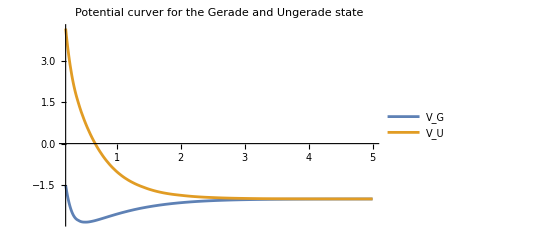

4.

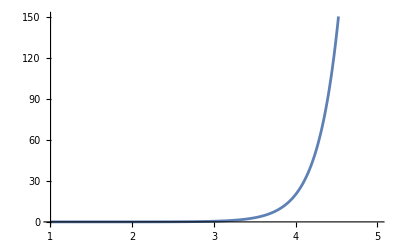

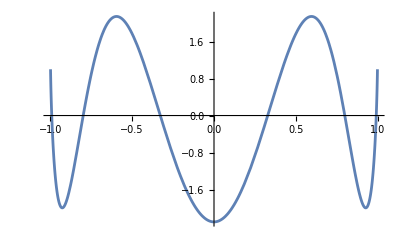

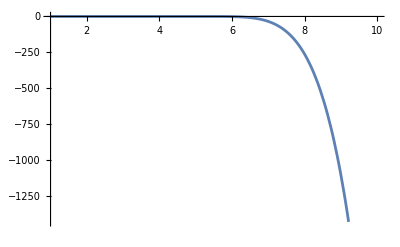

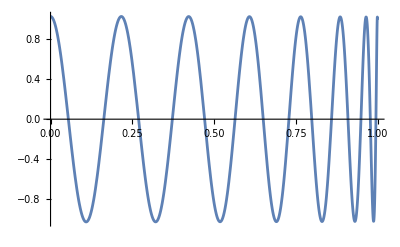

dInt =-1.48061×10^19

```mathematica
(* Radiative Quenching, Chapter 3 *)
(* This one uses my paper *)

(*electron mass *)
Subscript[m, e]=1;
(* Proton Mass *)
Subscript[m, p]=1836;
(* Reduced Mass *)
μ=Subscript[m, p]/2;
hbar= 1;  
hbarSI =1.054571817*^-34;
cLight=137.036 ;(*SpeedOfLight, atomic units*)
cLightSI= 299792458 ;(*SpeedOfLight, m/s*)
oneSec = 2.418884326509*^-17;  (* 1 sec SI <-> 1 sec AU *)
aBorh = 5.29177*^-11;   (* Si <-> AU *)

(* RawData format R,E, E + 1/R,A,p *)

vSg1RawData = Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV3.mx"];
vSu2RawData = Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/ungerade1sV3.mx"];


vSg1Data =vSg1RawData[[1;;44]];
vSu2Data = vSu2RawData[[1;;44]];

(* Calculate the Transition Dipole Moment *)
(* Upper Limit for integration *)
maxR = vSg1Data[[Length[vSg1Data]]][[1]];
Print["maxR=",maxR]
maxR = 5;
maxIndex = 12;

(* Load Potential curves for 1sg, 2sg states 
"R,E, E + 1/R,A,p *)
(* 1sg state, potential curve *)
vG=Interpolation[Transpose[{vSg1Data[[All,1]],vSg1Data[[All,3]]}], InterpolationOrder->3];
(* 2sg state, potential curve *)
vU=Interpolation[Transpose[{vSu2Data[[All,1]],vSu2Data[[All,3]]}], InterpolationOrder->3];

Plot[{vG[r],vU[r]},{r,0.2,maxR}, PlotRange->Full, PlotLegends->{"V_G","V_U"}, PlotLabel->"Potential curver for the Gerade and Ungerade state"]

R = vSg1Data[[16,1]]
a1=vSg1Data[[16,4]];
p1=vSg1Data[[16,5]];
a2=vSu2Data[[16,4]];
p2=vSu2Data[[16,5]];

maxDistance = 5;

ll1=NDSolveValue[{(ξ^2-1)L''[ξ]+ξ * L'[ξ]+ (a1 +2 R ξ -p1^2 ξ^2)L[ξ]==0 ,L[1.001]==0,L'[1.001]==1 },L,{ξ,1.001,maxDistance}];
mm1a=NDSolveValue[{(1-η^2)M''[η]-η *M'[η] + (a1 + p1^2 η^2)M[η]==0, M'[0]==0,M[.999]==1}, M,{η,0,.999}];
(* 2s wavefunction *) 
ll2=NDSolveValue[{(ξ^2-1)L''[ξ]+ξ * L'[ξ]+ (a2+2 R ξ -p2^2 ξ^2)L[ξ]==0 ,L[1.001]==0,L'[1.001]==1 },L,{ξ,1.001,maxDistance}];
mm2=NDSolveValue[{(1-η^2)M''[η]-η *M'[η] + (a2 + p2^2 η^2)M[η]==0, M'[0]==0,M[0.999]==1}, M,{η,0,.999}];

mm1[x_]:=If[x>=0,mm1a[x],mm1a[-x]];

Plot[ll1[x], {x, 1.001,5}]
Plot[mm1a[x],{x,-.999,.999}]


Plot[ll2[x], {x, 1.001,10}]
Plot[mm2[x],{x,0,.999}]

norm1=Sqrt[NIntegrate[Abs[ll1[ξ] mm1[η]]^2,{η,-.999,.999},{ξ,1.001,maxDistance}]];

llmm1[ξ_,η_]:=ll1[ξ]mm1[η];
llmm2[ξ_,η_]:=ll2[ξ]mm2[η];

dInt=(R/2)^3 NIntegrate[Conjugate[llmm1[ξ,η]]ξ η llmm2[ξ,η]((ξ^2-η^2)/(√(ξ^2-1)√(1-η^2))),{η,-0.999,0.999},{ξ,1.001,3}];

Print["dInt =", dInt]
```

```mathematica
(* Compute the Dipole momement D(r) for the single value of R *)
singleDR[R_,a1_,p1_,a2_,p2_, maxDistance_]:=Module[{norm1, norm2,dInt, l1,l2,m1,m2,lmNorm1, lmNorm2},
(* 1s wavefunction *)
l1=NDSolveValue[{(ξ^2-1)L''[ξ]+ξ * L'[ξ]+ (a1 +2 R ξ -p1^2 ξ^2)L[ξ]==0 ,L[1.001]==0,L'[1.001]==1 },L,{ξ,1.001,maxDistance}];
m1=NDSolveValue[{(1-η^2)M''[η]-η *M'[η] - (-a1 + p1^2 η^2)M[η]==0, M[0]==0,M'[0]==1}, M,{η,-.999,.999}];
(* 2s wavefunction *) 
l2=NDSolveValue[{(ξ^2-1)L''[ξ]+ξ * L'[ξ]+ (a2+2 R ξ -p2^2 ξ^2)L[ξ]==0 ,L[1.001]==0,L'[1.001]==1 },L,{ξ,1.001,maxDistance}];
m2=NDSolveValue[{(1-η^2)M''[η]-η *M'[η] - (-a2 + p2^2 η^2)M[η]==0, M[0]==1,M'[0]==0}, M,{η,-.999,.999}];

Print["R=",R];
(* Compute <ψ|ψ> = <Subscript[ψ, 1s]|Subscript[ψ, 1s]> + <Subscript[ψ, 2s]|Subscript[ψ, 2s]> *)
(* <Subscript[ψ, 1s]|Subscript[ψ, 1s]> *)
norm1=Sqrt[NIntegrate[Abs[l1[ξ] m1[η]]^2,{η,-.999,.999},{ξ,1.001,maxDistance}]];
(* <Subscript[ψ, 2s]|Subscript[ψ, 2s]> *)
norm2=Sqrt[NIntegrate[Abs[l2[ξ]m2[η]]^2,{η,-.999,.999},{ξ,1.001,maxDistance}]];

lmNorm1[ξ_,η_]:=1/norm1 l1[ξ]m1[η];
lmNorm2[ξ_,η_]:=1/norm2 l2[ξ]m2[η];

dInt=(R/2)^3 NIntegrate[Conjugate[lmNorm1[ξ,η]]ξ η lmNorm2[ξ,η]((ξ^2-η^2)/(√(ξ^2-1)√(1-η^2))),{η,-0.999,0.999},{ξ,1.001,maxDistance}];
{R,dInt }
];

(*singleDR[vSg1Data[[24]][[1]],vSg1Data[[19]][[4]],vSg1Data[[19]][[5]],vSu2Data[[19]][[4]],vSu2Data[[19]][[5]],5]
singleDR[vSg1Data[[14]][[1]],vSg1Data[[19]][[4]],vSg1Data[[19]][[5]],vSu2Data[[19]][[4]],vSu2Data[[19]][[5]],5]
singleDR[vSg1Data[[15]][[1]],vSg1Data[[20]][[4]],vSg1Data[[20]][[5]],vSu2Data[[20]][[4]],vSu2Data[[20]][[5]],5]*)
```

```mathematica
(* Get all Rs, and coefficients A and p and calculate D(R) for all Rs *)
(* RawData format R,E, E + 1/R,A,p *)
inputData = Transpose[{vSg1Data[[1;;maxIndex,1]],vSg1Data[[1;;maxIndex,4]],vSg1Data[[1;;maxIndex,5]],vSu2Data[[1;;maxIndex,4]],vSu2Data[[1;;maxIndex,5]]}];

allDR =Map[singleDR[#[[1]],#[[2]],#[[3]],#[[4]],#[[5]], maxR] &, inputData];
```

R=0.2

R=0.3

R=0.4

R=0.5

R=0.6

R=0.7

R=0.8

R=0.9

R=1.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.21233×10^-9 and 1.31884×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00229192 and 1.37144×10^-6 for the integral and error estimates.

R=1.1

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.13346×10^-9 and 3.42538×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

R=1.5

R=2.

```mathematica
allDR // MatrixForm
```

(0.2 | -0.0893696
0.3 | -0.13213
0.4 | -0.384232
0.5 | 0.0254169
0.6 | -0.406694
0.7 | 1.78895
0.8 | 0.522647
0.9 | -1.98178
1. | -1.3272
1.1 | -9.10647
1.5 | -45.9815
2. | -133.675
2.5 | -211.581
3. | -532.668
3.5 | -106.561
4. | 827.81
4.5 | 1550.91
5. | 137.769
6 | 594.81
7 | -22947.6
8 | -36928.8
9 | -53711.6
10 | -74750.3
11 | -5020.49)

{{0.2,7.17565×10^-33},{0.3,-1.82589×10^-32},{0.4,-4.22252×10^-32},{0.5,-7.7928×10^-32},{0.6,-1.24043×10^-31},{0.7,-1.82408×10^-31},{0.8,2.63181×10^-31},{0.9,-3.32698×10^-30},{1.,-2.42887×10^-33},{1.1,9.17199×10^-33},{1.5,-5.90727×10^-29},{2.,-1.04254×10^-30}}

InterpolatingFunction::dmval: Input value {0.1001} lies outside the range of data in the interpolating function. Extrapolation will be used.

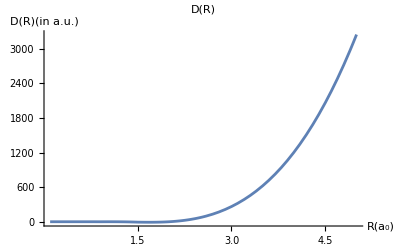

InterpolatingFunction::dmval: Input value {0.1001} lies outside the range of data in the interpolating function. Extrapolation will be used.

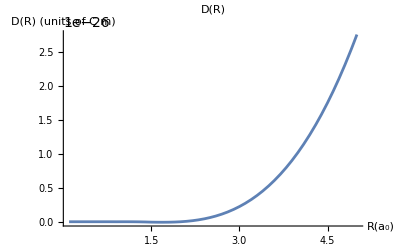

```mathematica
(* Dipole moment in SI units *)
drAUtoSI = 8.478*^-30; (* Cm *)
allDRSI=allDR;
allDRSI[[All,2]] =allDR[[All,2]]*drAUtoSI;
allDRSI

dR =Interpolation[Transpose[{allDR[[All,1]],allDR[[All,2]]}], InterpolationOrder->3];
Plot[dR[r],{r,0.1, maxR}, PlotLabel->"D(R)", AxesLabel->{"R(a_0)", "D(R)(in a.u.)"}, PlotRange->Full]

dRSI =Interpolation[Transpose[{allDRSI[[All,1]],allDRSI[[All,2]]}], InterpolationOrder->3];
Plot[dRSI[r],{r,0.1, maxR}, PlotLabel->"D(R)", AxesLabel->{"R(a_0)", "D(R) (units of C m)"}, PlotRange->Full, Axes->True]
```

```mathematica
aR[R_]:=4/(3hbar cLight^3)(dR[R])^2((vU[R]-vG[R])/hbar)^3;

aRAUtoSI = 4.1341*^16;
aRSI[R_]:=aR[R]*aRAUtoSI;

aRSI2[R_]:=4/(3 hbarSI cLightSI^3)(dRSI[R])^2(((vU[R]-vG[R])4.35974*^-18)/hbarSI)^3;


Plot[aR[r],{r,.1,  10}, PlotLabel->"A(R)", AxesLabel->{"R(a_0)", "A(R)"}, PlotRange->Full]
Plot[aRSI[r],{r,.1,  10}, PlotLabel->"A(R)", AxesLabel->{"R(a_0)", "A(R) (s^-1)"}, PlotRange->Full]
Plot[aRSI2[r],{r,.1,  10}, PlotLabel->"A(R)", AxesLabel->{"R(a_0)", "A(R) (s^-1)"}, PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {0.100202} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.12061} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.32265} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

InterpolatingFunction::dmval: Input value {0.100202} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.12061} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.32265} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

InterpolatingFunction::dmval: Input value {0.100202} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.12061} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.32265} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-